g1: Sale el mismo valor que para el código

-2.07889

sumaTR:

1.

transmisión:

0.660926

reflexión:

0.339074

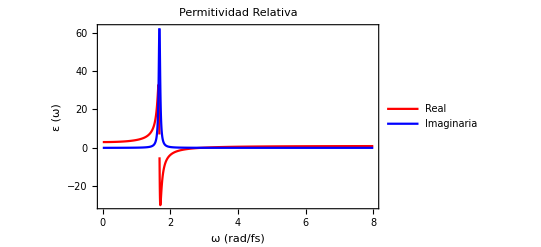

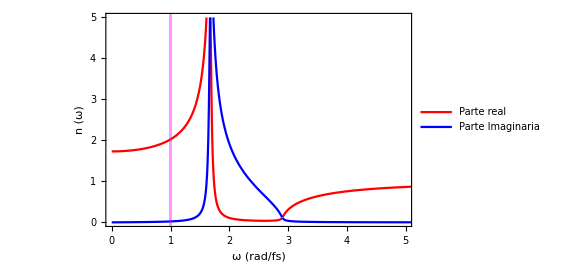

-Graphics-

```mathematica
w=1.5; (*Puslo láser*)
(*Parámetros del oscilador, los mismo que en el programa*)
f1=0.4/w;
w=w/w;
delta1=0.1*f1;
w1=2*Pi*f1;
εs=3;
εinf=1;
G1=1;
b1=G1*(εs-εinf);

deltatime=0.1;
a1=2+2*delta1*deltatime+(w1^2)*(deltatime^2)*(1+b1);
c1=(w1^2)*(deltatime^2)*b1;
"g1: Sale el mismo valor que para el código"
g1=-2+2*delta1*deltatime-(w1^2)*(deltatime^2)*(1+b1)

(*Función: Permitvidad relativa*)
εr[w_]:=εinf+((εs-εinf)*w1^2)/(w1^2-2*I*w*delta1-w^2);
n1=1; (*índice de refracción del vacío*)
(*Sustituimos*)
n2[w_]:=Abs[Sqrt[εr[w]]];
coefT=(4*n2[w]*n1)/(n1+n2[w])^2;
coefR=Abs[(n2[w] -n1)/(n1+n2[w])]^2 ;
"sumaTR:"
sumaTR=coefT+coefR
"transmisión:"
coeft=(2*n1)/(n1+n2[w])
"reflexión:"
coefr=(n2[w] -n1)/(n1+n2[w])

Plot[{Re[εr[w]],Im[εr[w]]},{w,0,8},PlotRange->All, PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]}, Frame->True,FrameLabel->{"ω (rad/fs)","ε (ω)"," "," "},PlotLabel->Style["Permitividad Relativa",16,Black],FrameStyle->{Black,Black,Black,Black},PlotLegends->{"Real","Imaginaria"}]
a=Plot[{Re[Sqrt[εr[w]]],Im[Sqrt[εr[w]]]},{w,0,10},PlotRange->{{0,5},{0,5}}, PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]}, Frame->True,FrameLabel->{"ω (rad/fs)","n (ω)"," "," "},FrameStyle->{Black,Black,Black,Black},PlotLegends->Placed[{"Parte real","Parte Imaginaria"},{Scaled[{0.55,0.8}], {0, 0.8}}], GridLines->{{{w,Directive[RGBColor[1,0,1],Thickness[0.005]]}},None}]
partereal=Table[{w,Re[Sqrt[εr[w]]]},{w,0,5,0.00005}];
parteimag=Table[{w,Im[Sqrt[εr[w]]]},{w,0,5,0.00005}];
ListPlot[{partereal,parteimag},PlotRange->{{0,5},{0,7}}, PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]},Joined->True, Frame->True,FrameLabel->{"ω (rad/fs)","n (ω)"," "," "},FrameStyle->{Black,Black,Black,Black},PlotLegends->Placed[{"Parte real","Parte Imaginaria"},{Scaled[{0.6,0.85}], {0, 0.8}}], GridLines->{{{w,Directive[RGBColor[1,0,1],Thickness[0.005]]}},None}]
```

He comprobado que a1, c1 y g1 son los mismos resultados que para el código en C.
Comparamos los valores obtenidos en Mathematica con los valores máximos y mínimos de la transmitida y reflejada del código en C para un tiempo justo después de atravesar la discontinuidad.

Parámetros | t teórico (coefr) | r teórico (coeft) | t código | r código | Error rel t % | error rel r%
f1=0.05,delta1=0.5*f1,w1=1 | 0.938525 | -0.0614747 | 0.925661 | -0.069131 | 1.3 | 12
f1=0.05,delta1=0.5*f1,w1=2 | 0.987029 | -0.0129706 | 0.983763 | -0.0130642 | 0.33 | 9
f1=0.05,delta1=0.5*f1,w1=6 | 0.998622 | -0.00137824 | 0.996972 | -0.0147102 | 0.17 | 6.73
f1=0.05,delta1=0.5*f1,w1=0.5 | 0.737948 | -0.262052 | 0.346295 | -0.499136 | 50 | 90
f1=1,delta1=0.5*f1,w1=0.1 | 0.732012 | -0.267988 | 0.708194 | -0.260722 | 3.25 | 2.711

## Cálculo del valor del segundo armónico

```mathematica
(*Resonancia del medio dispersivo*)
εs=10;
εinf=8;
G1=1;
b1=G1*(εs-εinf);

f1=0.01*10^15; (*Hz/s*)
delta1=0.5*f1; (*Hz/s*)
w1=2*Pi*f1; (*rad/s*)

w=4*10^15; (*rad/s*)(*Puslo láser*)
εr[w_]:=εinf+((εs-εinf)*w1^2)/(w1^2-2*I*w*delta1-w^2);
(*Sustituimos*)
n2[w_]:=Abs[Sqrt[εr[w]]]
n2[w]
c=3*10^8 ;(*m/s*)
"Ajuste de fase"
Δk=(2*w(n2[w]-n2[2*w]))/c
"Longitud total de la simulación en metros"
deltatime=0.01*10^-15;
size=3500;
nodos1=50;
distancia1=c*deltatime*nodos1
"espaciado"
espaciadonodos1=c*deltatime (*m*)
nodos2=size-nodos1;
v2=c/n2[w]
distancia2=v2*deltatime*nodos2
"espaciado"
espaciadonodos2=v2*deltatime (*m*)
"tiempos"
t1=deltatime*nodos1
t2=deltatime*nodos2
L=distancia1+distancia2 (*Longitud de la simulación*)
"Intensidad del segundo armónico en el punto L"
intenw=1;
deff=1;
e0=8.854*10^-12 ; (*F/m*)
intensidad=L^2*(Sin[Δk*L/2]/(Δk*L/2))^2 (*(8*w^2*deff^2*intenw^2)/(n2[w]^2*n2[2*w]*e0*c^2)*)
```

2.82834

Ajuste de fase

-1745.27

Longitud total de la simulación en metros

1.5×10^-7

espaciado

3.×10^-9

1.06069×10^8

3.65939×10^-6

espaciado

1.06069×10^-9

tiempos

5.×10^-16

3.45×10^-14

3.80939×10^-6

Intensidad del segundo armónico en el punto L

1.45114×10^-11

```mathematica
Δk1[w_]:=(2*w(n2[w]-n2[2*w]))/c;
a[w_]:=(Sin[Δk1[w]*L/2]/(Δk1[w]*L/2))^2;
Plot[a[w],{w,4.5*10^15,4.7*10^15},PlotRange->All]
```

SetDelayed::write: Tag Legended in … is Protected.

-Graphics-